```mathematica
DSolve[{p V'[t]==ν[t] R T'[t]+R T[t] ν'[t],P==p V'[t]+5/2 ν[t]R T'[t],ν[0]==ν0,V[0]==(ν0 R T0)/p},{ν,V},t]//FullSimplify
```

{{V→Function[{t},1/(7 p α (T0+t α)^(5/2))(-2 P T0^(7/2)+2 P T0^3 √(T0+t α)+6 P t T0^2 α √(T0+t α)+6 P t^2 T0 α^2 √(T0+t α)+2 P t^3 α^3 √(T0+t α)+7 R T0^(7/2) α ν0)],ν→Function[{t},1/(7 R α (T0+t α)^(7/2))(-2 P T0^(7/2)+2 P T0^3 √(T0+t α)+6 P t T0^2 α √(T0+t α)+6 P t^2 T0 α^2 √(T0+t α)+2 P t^3 α^3 √(T0+t α)+7 R T0^(7/2) α ν0)]}}

```mathematica
Clear[T,ν,V]
```

```mathematica
T[t_]:=T0+α t
```

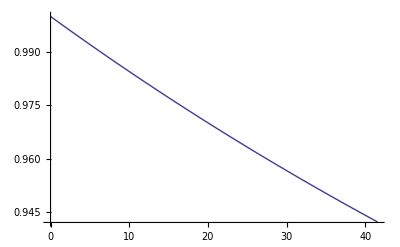

```mathematica
Plot[ν[t]/.%45/.p->10^5/.α->20/41.55/.P->10/.T0->300/.ν0->1/.R->8.314,{t,0,41.55}]
```

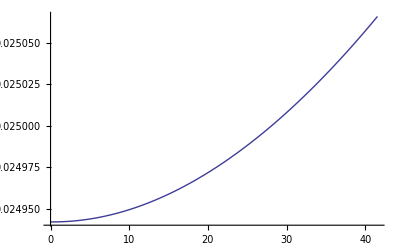

```mathematica
Plot[V[t]/.%45/.p->10^5/.α->20/41.55/.P->10/.T0->300/.ν0->1/.R->8.314,{t,0,41.55}]
```